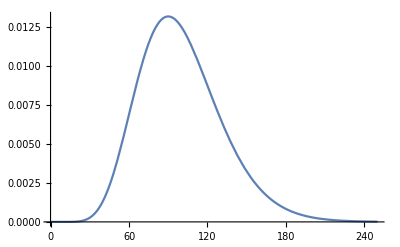

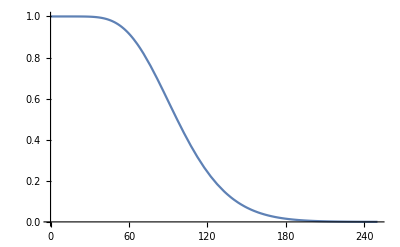

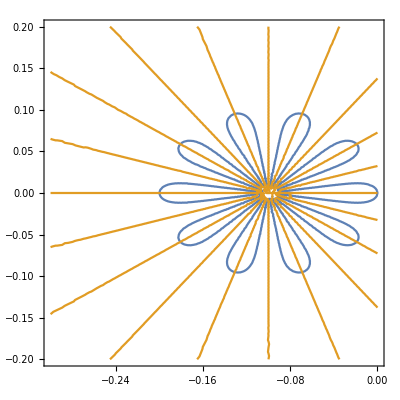

ConditionalExpression[1-(b^a x^a (b ⅇ^((2 ⅈ π)/a) x)^-a (Gamma[a]-Gamma[a,b ⅇ^((2 ⅈ π)/a) x]))/Gamma[a],Re[a]>0]

ConditionalExpression[(ⅇ^(b (-1+ⅇ^((2 ⅈ π)/a)) x) Gamma[a] (1-(b^a x^a (b ⅇ^((2 ⅈ π)/a) x)^-a (Gamma[a]-Gamma[a,b ⅇ^((2 ⅈ π)/a) x]))/Gamma[a]))/Gamma[a,b x],Re[a]>0]

ConditionalExpression[1/Gamma[a,b x]ⅇ^(b (-1+ⅇ^((2 ⅈ π)/a)) x) Gamma[a] (-(b^(-1+a) ⅇ^(-b ⅇ^((2 ⅈ π)/a) x) x^a)/Gamma[a]+(a b^a ⅇ^((2 ⅈ π)/a) x^(1+a) (b ⅇ^((2 ⅈ π)/a) x)^(-1-a) (Gamma[a]-Gamma[a,b ⅇ^((2 ⅈ π)/a) x]))/Gamma[a]-(a b^(-1+a) x^a (b ⅇ^((2 ⅈ π)/a) x)^-a (Gamma[a]-Gamma[a,b ⅇ^((2 ⅈ π)/a) x]))/Gamma[a])+(ⅇ^(-b x+b (-1+ⅇ^((2 ⅈ π)/a)) x) x (b x)^(-1+a) Gamma[a] (1-(b^a x^a (b ⅇ^((2 ⅈ π)/a) x)^-a (Gamma[a]-Gamma[a,b ⅇ^((2 ⅈ π)/a) x]))/Gamma[a]))/Gamma[a,b x]^2+(ⅇ^(b (-1+ⅇ^((2 ⅈ π)/a)) x) (-1+ⅇ^((2 ⅈ π)/a)) x Gamma[a] (1-(b^a x^a (b ⅇ^((2 ⅈ π)/a) x)^-a (Gamma[a]-Gamma[a,b ⅇ^((2 ⅈ π)/a) x]))/Gamma[a]))/Gamma[a,b x],Re[a]>0]

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Resolve::bddom: Value {b,-11,11} of the domain argument should be Complexes, Reals, Algebraics, Rationals, Integers, Primes, Booleans, or Automatic.

```mathematica
param={a->10};
P[x_,b_]=x^(a-1)*Exp[-b*x]*b^a/Gamma[a];

S[x_,b_]=Gamma[a,b*x]/Gamma[a];

PL[s_,b_]=LaplaceTransform[P[x,b],x,s];

lambda[b_]=b*(Exp[2*Pi*I/a]-1);

Pplot=P[x,0.1]/.param;
Splot=S[x,0.1]/.param;
PLplot=PL[s,0.1]/.param;

s=u+I*v;

Plot[Pplot,{x,0,250}]
Plot[Splot,{x,0,250}]

ContourPlot[{Re[PLplot]==1,Im[PLplot]==0},{u,-0.3,0},{v,-0.2,0.2}]


Phi[x_,b_]=(b+lambda[b])^(a+1)/(a*b^a)*S[x,b]*Exp[-lambda[b]*x];
F[x_,b_]=(1-Integrate[P[o,b]*Exp[-lambda[b]*o],{o,0,x}])


Psi[x_,b_]=(S[x,b])^(-1)*Exp[lambda[b]*x]*F[x,b]

D[Psi[x,b],b]
```